## Fourier Series

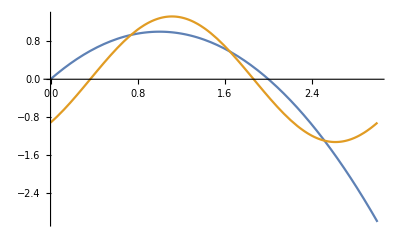

(3 sin((2 π x)/3))/π-(9 cos((2 π x)/3))/π^2

```mathematica
Clear[x,a,b,f,l,n]
f[x_]=2x-x^2;(* the approximated function *)
l = 3 ;(* Length of periode *)
aa = 0;  (* for intarval [a, a+l] *)
n =1; (* number of eterations *)
a[0]=Integrate[f[x],{x,aa,aa+l}]/l;
Do[a[i]=2 1/l Integrate[f[x]Cos[(2π i)/l x],{x,aa,aa+l}];b[i]=2 1/l Integrate[f[x]Sin[(2π i x)/l],{x,aa,aa+l}],{i,1,n}]
Approxemation[x_] = Sum[a[i]Cos[(2π i x)/l]+b[i]Sin[(2π i x)/l],{i,0,n}];
Plot[{f[x],Approxemation[x]},{x,aa,aa+l}]
Approxemation[x]//TraditionalForm
```

```mathematica
Table[{a[i],b[i]},{i,0,n}]//TableForm
```

0 | b[0]
-9/π^2 | 3/π

```mathematica
f[0.5]-Approxemation[.5]//Abs
```

0.378952

## Least Square Fits and Interpolating at equal Space

```mathematica
Clear[x,f,m,y,a,b,T,t]
f[0]=1;
f[x_]=Sin[x]/x;
m=20;
x[i_]=(i π)/m;
y[i_]:=f[x[i]];
a[0]=1/(2m)∑_(i=0)^(2m-1) y[i];
a[k_]:=If[k≠m,1/m∑_(i=0)^(2m-1) y[i]Cos[x[i] k],1/(2m)∑_(i=0)^(2m-1) y[i]Cos[x[i]m]];
b[k_]:=1/m∑_(i=0)^(2m-1) y[i]Sin[x[i] k];
T[t_]=a[0]+Sum[a[j]Cos[x j],{j,1,m}]+Sum[b[j]Sin[x j],{j,1,m-1}];
T[x]//N//TraditionalForm
```

0.49501 sin(x)+0.170388 sin(2. x)+0.107622 sin(3. x)+0.0783836 sin(4. x)+0.0610858 sin(5. x)+0.0494851 sin(6. x)+0.041059 sin(7. x)+0.0345843 sin(8. x)+0.0293929 sin(9. x)+0.0250875 sin(10. x)+0.0214166 sin(11. x)+0.0182121 sin(12. x)+0.0153569 sin(13. x)+0.0127662 sin(14. x)+0.0103765 sin(15. x)+0.00813868 sin(16. x)+0.00601306 sin(17. x)+0.0039667 sin(18. x)+0.001971 sin(19. x)+0.262589 cos(x)+0.0410015 cos(2. x)+0.0313076 cos(3. x)+0.0284478 cos(4. x)+0.0272046 cos(5. x)+0.02655 cos(6. x)+0.0261629 cos(7. x)+0.0259152 cos(8. x)+0.0257476 cos(9. x)+0.0256294 cos(10. x)+0.0255435 cos(11. x)+0.0254796 cos(12. x)+0.0254315 cos(13. x)+0.0253949 cos(14. x)+0.0253671 cos(15. x)+0.0253463 cos(16. x)+0.0253312 cos(17. x)+0.0253209 cos(18. x)+0.025315 cos(19. x)+0.0126565 cos(20. x)+0.238258

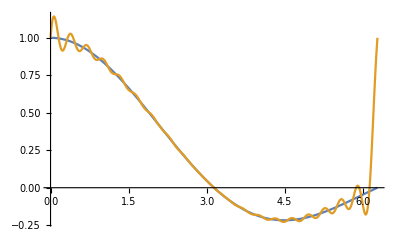

```mathematica
Plot[{f[x],T[x]},{x,0,2π}]
```